### Introduction

This Mathematica notebook is licensed under a  .

It provides software for producing the endograph of finite functions.   gives a definition of endograph and  discusses finite endographs.

The notebook is still rough and incomplete.  It will be revised from time to time.  I hope anyone interested will feel free to improve this work and to use it in their own publications and coursework.

### Definitions

```mathematica
SetOptions[Plot, AspectRatio -> Automatic]; 
tf := TableForm; tx := TeXForm; hh := Hold; 
  ss := Simplify; 
tt[x_] :=TraditionalForm[x]; 
  mf := MatrixForm;
```

```mathematica
RuleGraph[r_]:=GraphPlot[r,VertexLabeling->True, DirectedEdges->True,EdgeRenderingFunction->(Arrow[#1,0.1]&),PlotStyle->Directive[Arrowheads[0.02]],VertexRenderingFunction->(Text[#2,#1]&),ImageSize->Medium]
```

```mathematica
MakeFunctionRule[f_,n_]:=#->f[#]&/@ Table[k,{k,0,n-1}]
```

```mathematica
Endograph[f_,n_]:=GraphPlot[MakeFunctionRule[f,n],VertexLabeling->True,DirectedEdges->True,EdgeRenderingFunction->(Arrow[#1,0.1]&),PlotStyle->Directive[Arrowheads[0.02]],VertexRenderingFunction->(Text[#2,#1]&),ImageSize->Small]
```

```mathematica
LGraph[r_]:=LayeredGraphPlot[r,EdgeRenderingFunction->(Arrow[#1,0.1]&),PlotStyle->Directive[Arrowheads[0.03]],VertexRenderingFunction->(Text[#2,#1]&),ImageSize->Small]
```

```mathematica
DFGraph[f_,n_]:=LGraph[MakeFunctionRule[f,n]]
```

```mathematica
CographSource[n_]:=n;CographTarget[n_]:=n+100  (*See the failed experiment at the end of this notebook*)
```

```mathematica
CographFunctionRule[f_,n_]:=CographSource[#]->CographTarget[f[#]]&/@ Table[k,{k,0,n-1}]
```

```mathematica
CographLayout[n_]:=(CographSource[#]&/@Table[k,{k,0,4}])~Union~(CographTarget[#]&/@Table[k,{k,0,4}])
```

```mathematica
CR[n_]:=If[n<100,{n,2},{n-100,0}]
```

```mathematica
Lab[n_]:=If[n<100,n,n-100]
```

```mathematica
Cograph[f_,n_]:=GraphPlot[CographFunctionRule[f,n],VertexLabeling->True,DirectedEdges->True,EdgeRenderingFunction->(Arrow[#1,0.1]&),PlotStyle->Directive[Arrowheads[0.04]],VertexCoordinateRules->Evaluate[(#->CR[#])&/@ CographLayout[n]],VertexRenderingFunction->(Text[Lab[#2],#1]&),ImageSize->Small]
```

```mathematica
f1[n_]:=Mod[n+1,5];f2[n_]:=Mod[n^2,5];
```

```mathematica
t2[1]:=2;t2[2]:=4;t2[4]:=1;t2[3]:=0;t2[0]:=3;t2[n_]:=n
```

#### Some Checking

```mathematica
CographFunctionRule[t2,5]
```

{0→103,1→102,2→104,3→100,4→101}

```mathematica
CographSource[#]&/@Table[k,{k,0,4}]
```

{0,1,2,3,4}

```mathematica
CographTarget[#]&/@Table[k,{k,0,4}]
```

{100,101,102,103,104}

```mathematica
CographLayout[5]
```

{0,1,2,3,4,100,101,102,103,104}

```mathematica
#->CR[#]&/@ CographLayout[5]
```

{0→{0,2},1→{1,2},2→{2,2},3→{3,2},4→{4,2},100→{0,0},101→{1,0},102→{2,0},103→{3,0},104→{4,0}}

### Permutations

```mathematica
t1[1]:=2;t1[2]:=1;t1[n_]:=n
```

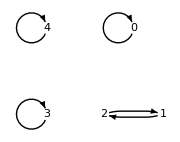

```mathematica
Endograph[t1,5]
```

```mathematica
t2[1]:=2;t2[2]:=4;t2[4]:=1;t2[3]:=0;t2[0]:=3;t2[n_]:=n
```

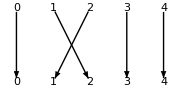

```mathematica
Cograph[t1,5]
```

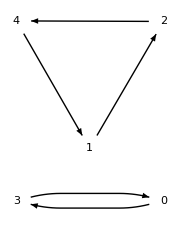

```mathematica
Endograph[t2,5]
```

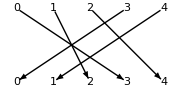

```mathematica
Cograph[t2,5]
```

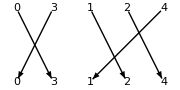

```mathematica
GraphPlot[CographFunctionRule[t2,5],VertexLabeling->True,DirectedEdges->True,EdgeRenderingFunction->(Arrow[#1,0.1]&),PlotStyle->Directive[Arrowheads[0.04]],VertexCoordinateRules->{0->{0,2},1->{2,2},2->{3,2},3->{1,2},4->{4,2},100->{0,0},101->{2,0},102->{3,0},103->{1,0},104->{4,0}},VertexRenderingFunction->(Text[Lab[#2],#1]&),ImageSize->Small]
```

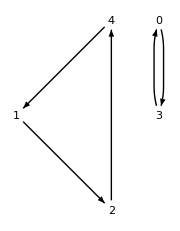

```mathematica
DFGraph[t2,5]
```

### Tree Structure

```mathematica
f3[n_]:=Mod[2n^9+5n^8+n^7+4n^6+9n^5+1,11]
```

```mathematica
2n^9+5n^8+n^7+4n^6+9n^5+1//TeXForm
```

2 n^9+5 n^8+n^7+4 n^6+9 n^5+1

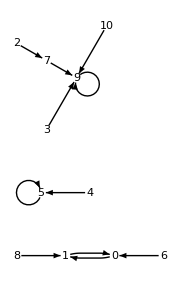

```mathematica
Endograph[f3,11]
```

```mathematica
CographFunctionRule[f3,11]
```

{0→101,1→100,2→107,3→109,4→105,5→105,6→100,7→109,8→101,9→109,10→109}

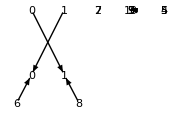

```mathematica
Cograph[f3,11]
```

```mathematica
f4[n_]:=Mod[2n^9+5n^8+n^7+4n^6+9n^5+6,11]
```

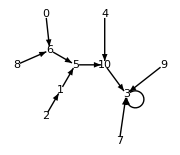

```mathematica
Endograph[f4,11]
```

```mathematica
f5[n_]:=Mod[2n^9+2n^8+n^7+4n^6+n^5+n^3+6n^2+6,11]
```

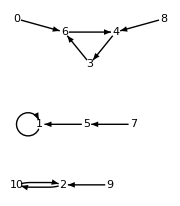

```mathematica
Endograph[f5,11]
```

```mathematica
ru1:={1->2,2->3,3->4,4->1,5->2,6->2,7->6,8->6,9->4,10->9,11->9,12->11,0->11,13->3,14->4,15->4,16->15}
```

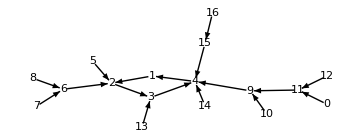

```mathematica
RuleGraph[ru1]
```

### Involutions

```mathematica
ru2:={1->2,2->1,3->3,4->4,5->6,6->5}
```

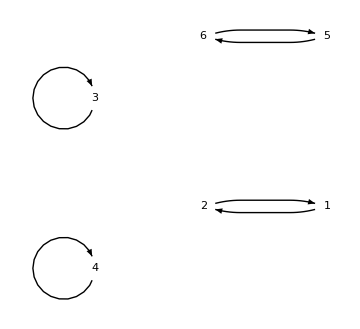

```mathematica
RuleGraph[ru2]
```

```mathematica
ru3:={1->1,2->2,3->3,4->4,5->2,6->2,7->6,8->6,9->4,10->9,11->9,12->11,0->11,13->3,14->4,15->4,16->15}
```

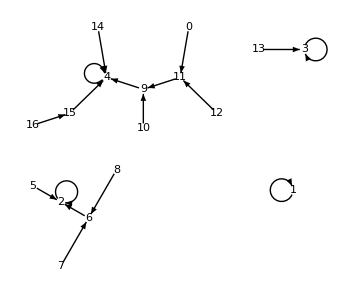

```mathematica
RuleGraph[ru3]
```

```mathematica
f7[x_]:=x/.ru3
```

```mathematica
Table[{x,f7[x]},{x,0,16}]
```

{{0,11},{1,1},{2,2},{3,3},{4,4},{5,2},{6,2},{7,6},{8,6},{9,4},{10,9},{11,9},{12,11},{13,3},{14,4},{15,4},{16,15}}

```mathematica
Table[{x,f7[f7[x]]},{x,0,16}]
```

{{0,9},{1,1},{2,2},{3,3},{4,4},{5,2},{6,2},{7,2},{8,2},{9,4},{10,4},{11,4},{12,9},{13,3},{14,4},{15,4},{16,4}}

### Idempotents

```mathematica
ru4:={1->1,2->2,3->3,4->4,5->4,6->4,7->3,8->2,9->1,10->1,11->1,12->2,13->2,14->2,15->3,16->3}
```

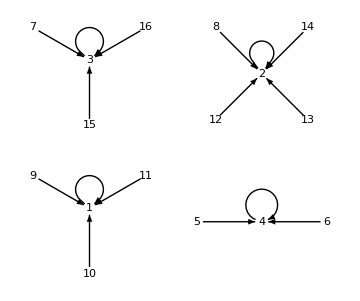

```mathematica
RuleGraph[ru4]
```

```mathematica
f8[x_]:=x/.ru4
```

```mathematica
Table[{x,f8[x],f8[f8[x]]},{x,0,16}]//tf
```

0 | 0 | 0
1 | 1 | 1
2 | 2 | 2
3 | 3 | 3
4 | 4 | 4
5 | 4 | 4
6 | 4 | 4
7 | 3 | 3
8 | 2 | 2
9 | 1 | 1
10 | 1 | 1
11 | 1 | 1
12 | 2 | 2
13 | 2 | 2
14 | 2 | 2
15 | 3 | 3
16 | 3 | 3

### Old Examples

#### Example 1

```mathematica
ru1:={a->a,c->d,b->c,d->a,e->d,f->e,g->b,h->d,i->h,j->e}
```

```mathematica
ru1
```

{a→a,c→d,b→c,d→a,e→d,f→e,g→b,h→d,i→h,j→e}

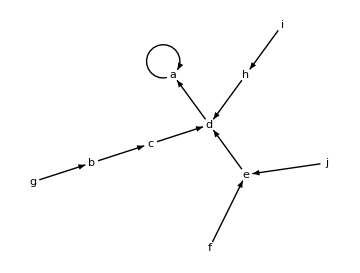

```mathematica
RuleGraph[ru1]
```

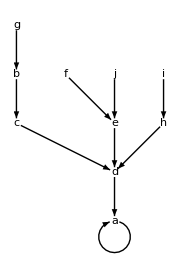

```mathematica
LGraph[ru1]
```

#### Example 2

```mathematica
g[n_]:=Mod[n^2+1,13]
```

```mathematica
MakeFunctionRule[g,13]
{0->1,1->2,2->5,3->10,4->4,5->0,6->11,7->11,8->0,9->4,10->10,11->5,12->2}
```

{0→1,1→2,2→5,3→10,4→4,5→0,6→11,7→11,8→0,9→4,10→10,11→5,12→2}

{0→1,1→2,2→5,3→10,4→4,5→0,6→11,7→11,8→0,9→4,10→10,11→5,12→2}

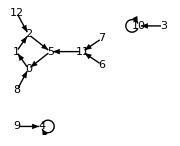

```mathematica
Endograph[g,13]
```

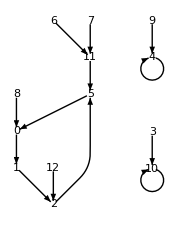

```mathematica
DFGraph[g,13]
```

```mathematica
h[n_]:=Mod[n^9,11]
```

#### Example 3

```mathematica
MakeFunctionRule[h,11]
{0->0,1->1,2->6,3->4,4->3,5->9,6->2,7->8,8->7,9->5,10->10}
```

{0→0,1→1,2→6,3→4,4→3,5→9,6→2,7→8,8→7,9→5,10→10}

{0→0,1→1,2→6,3→4,4→3,5→9,6→2,7→8,8→7,9→5,10→10}

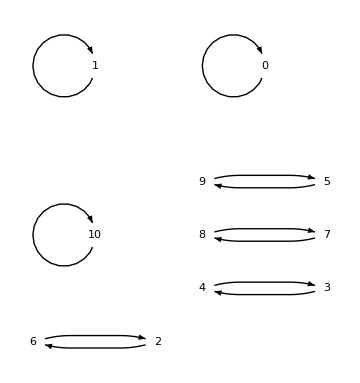

```mathematica
RuleGraph[MakeFunctionRule[h,11]]
```

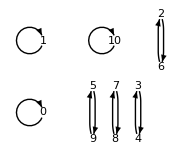

```mathematica
DFGraph[h,11]
```

#### Example 4

```mathematica
k[n_]:=Mod[n^9+n^7+5n,11]
```

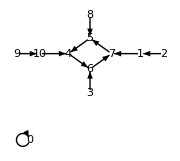

```mathematica
Endograph[k,11]
```

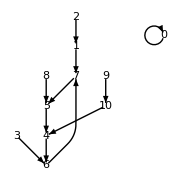

```mathematica
DFGraph[k,11]
```

#### Example 5

```mathematica
s[n_]:=Mod[(n+1)^9+n^7+5n,11]
```

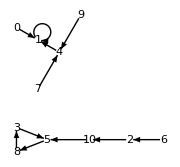

```mathematica
Endograph[s,11]
```

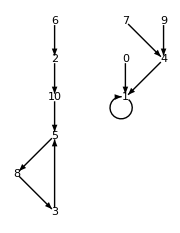

```mathematica
DFGraph[s,11]
```

```mathematica
aaa[n_]:=Mod[(n+1)^9+(n^+2)^7+5n,11]
```

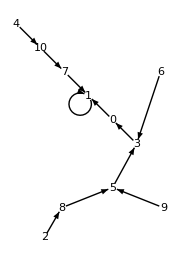

```mathematica
Endograph[aaa,11]
```

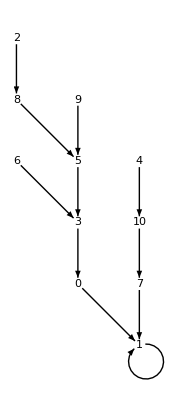

```mathematica
DFGraph[aaa,11]
```

```mathematica
bbb[n_]:=Mod[n^2+5,11]
```

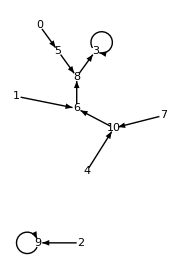

```mathematica
Endograph[bbb,11]
```

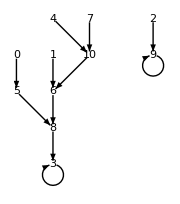

```mathematica
DFGraph[bbb,11]
```

```mathematica
ccc[n_]:=Mod[n^3+5,11]
```

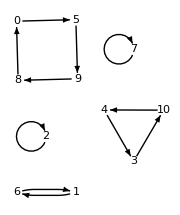

```mathematica
Endograph[ccc,11]
```

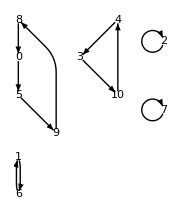

```mathematica
DFGraph[ccc,11]
```

```mathematica
x[n_]:=bbb[ccc[n]]
```

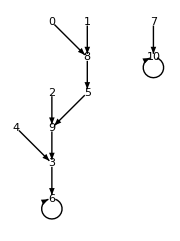
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{DFGraph[ccc,11], DFGraph[bbb,11], DFGraph[x,11]}
```

```mathematica
ddd[n_]:=Mod[n^3+n^2,11]
```

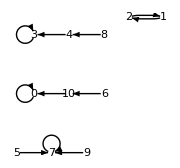

```mathematica
Endograph[ddd,11]
```

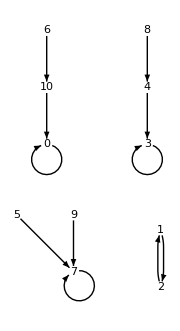

```mathematica
DFGraph[ddd,11]
```

```mathematica
p[n_]:=Mod[n^2+1,11]
```

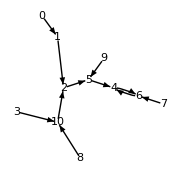

```mathematica
Endograph[p,11]
```

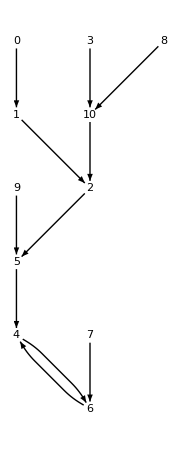

```mathematica
DFGraph[p,11]
```

```mathematica
pp[x_]:=p[p[x]]
```

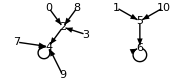

```mathematica
Endograph[pp,11]
```

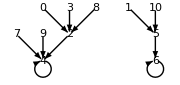

```mathematica
DFGraph[pp,11]
```

```mathematica
ppp[x_]:=p[p[p[x]]]
```

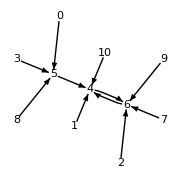

```mathematica
Endograph[ppp,11]
```

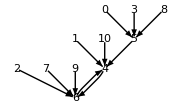

```mathematica
DFGraph[ppp,11]
```

```mathematica
dddOp[n_]:=ddd[p[n]]
```

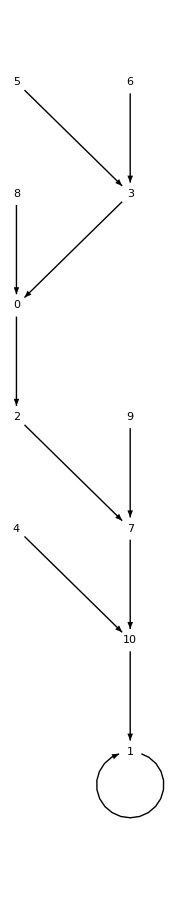

```mathematica
DFGraph[dddOp,11]
```

```mathematica
pOddd[n_]:=p[ddd[n]]
```

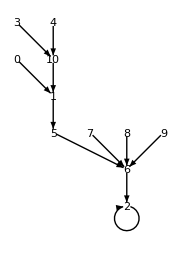
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{DFGraph[p,11], DFGraph[ddd,11], DFGraph[dddOp,11], DFGraph[pOddd,11]}
```

```mathematica
ht[n_]:=Mod[n^(11),13]
```

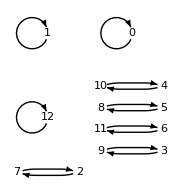

```mathematica
Endograph[ht,13]
```

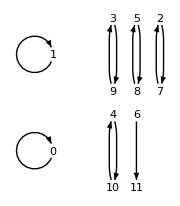

```mathematica
DFGraph[ht,11]
```

```mathematica
htx[n_]:=Mod[n^(11)+n^9+n^7+1,13]
```

```mathematica
htx[11]
```

4

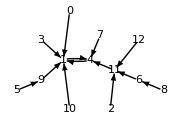

```mathematica
Endograph[htx,13]
```

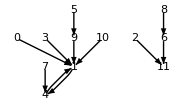

```mathematica
DFGraph[htx,11]
```

```mathematica
Table[{n,htx[n]},{n,0,12}]//tf
{{0, 1}, {1, 4}, {2, 11}, {3, 1}, {4, 1}, {5, 9}, {6, 11}, {7, 4}, {8, 6}, {9, 1}, {10, 1}, {11, 4}, {12, 11}}
```

0 | 1
1 | 4
2 | 11
3 | 1
4 | 1
5 | 9
6 | 11
7 | 4
8 | 6
9 | 1
10 | 1
11 | 4
12 | 11

{{0,1},{1,4},{2,11},{3,1},{4,1},{5,9},{6,11},{7,4},{8,6},{9,1},{10,1},{11,4},{12,11}}

```mathematica
fbig[0]:=5;fbig[1]:=2;fbig[2]:=13;fbig[3]:=4;fbig[4]=14;fbig[5]:=6;fbig[6]:=7;fbig[7]:=8;fbig[8]:=9;fbig[9]:=10;fbig[10]:=5;fbig[11]:=2;fbig[12]:=2;fbig[13]:=14;fbig[14]:=7;
```

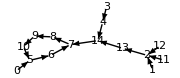

```mathematica
Endograph[fbig,15]
```

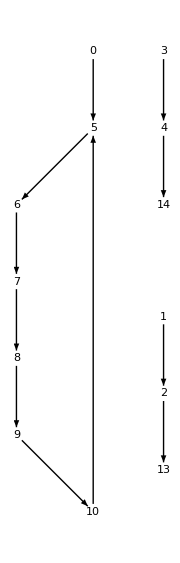

```mathematica
DFGraph[fbig,11]
```

```mathematica
uuu[n_]:=Mod[n^5+1,11];vvv[n_]:=Mod[n^6+1,11]; www[n_]:=uuu[vvv[n]];xxx[n_]:=vvv[uuu[n]]
```

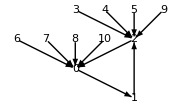
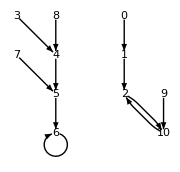
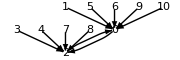
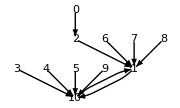

```mathematica
{DFGraph[uuu,11], DFGraph[vvv,11], DFGraph[www,11], DFGraph[xxx,11]}
```

```mathematica
uuu[n_]:=Mod[n^5,11];vvv[n_]:=Mod[n^6,11]; www[n_]:=uuu[vvv[n]];xxx[n_]:=vvv[uuu[n]]
```

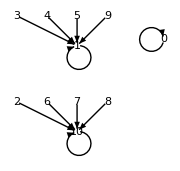
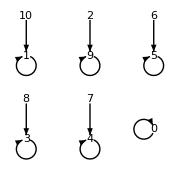
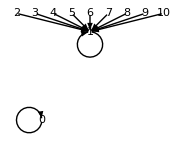
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{DFGraph[uuu,11], DFGraph[vvv,11], DFGraph[www,11], DFGraph[xxx,11]}
```

### Experiment: Why don’t this version of VertexCoordinateRules work?

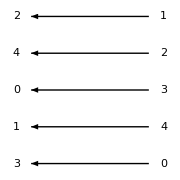

```mathematica
GraphPlot[{{0,2}->{3,0},{1,2}->{2,0},{2,2}->{4,0},{3,2}->{0,0},{4,2}->{1,0}},VertexLabeling->True,DirectedEdges->True,EdgeRenderingFunction->(Arrow[#1,0.1]&),PlotStyle->Directive[Arrowheads[0.04]],VertexCoordinateRules->{{0,0}->{0,0},{0,2}->{0,2},{1,0}->{1,0},{1,2}->{1,2},{2,0}->{2,0},{2,2}->{2,2},{3,0}->{3,0},{3,2}->{3,2},{4,0}->{4,0},{4,2}->{4,2}},VertexRenderingFunction->(Text[#2[[1]],#1]&),ImageSize->Small]
```

### Polynomials over finite fields

```mathematica
ru1:={1->2,2->3,3->4,4->1,5->2,6->2,7->6,8->6,9->4,10->9,11->9,12->11,0->11,13->3,14->4,15->4,16->15}
```

```mathematica
gr:={#,#/.ru1}&/@Table[n,{n,0,16}]
```

```mathematica
gr
```

{{0,11},{1,2},{2,3},{3,4},{4,1},{5,2},{6,2},{7,6},{8,6},{9,4},{10,9},{11,9},{12,11},{13,3},{14,4},{15,4},{16,15}}

```mathematica
t4[x_]:=PolynomialMod[InterpolatingPolynomial[gr,x,Modulus->17]//Expand,17]
```

```mathematica
t4[x]
```

11+15 x+4 x^2+14 x^3+16 x^4+15 x^5+14 x^6+x^7+9 x^8+4 x^9+14 x^10+5 x^11+10 x^12+3 x^13+x^14+13 x^15+6 x^16

```mathematica
t4[x]//tx
```

6 x^{16}+13 x^{15}+x^{14}+3 x^{13}+10 x^{12}+5
   x^{11}+14 x^{10}+4 x^9+9 x^8+x^7+14 x^6+15
   x^5+16 x^4+14 x^3+4 x^2+15 x+11

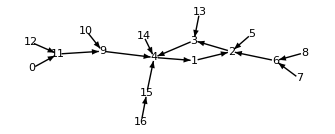

```mathematica
Endograph[t4,17]
```

```mathematica
RuleGraph[ru1]
```

-Graphics-